```mathematica
$LoadFeynArts= True;
<<FeynCalc`
SetDimensions[3];
```

FeynCalc is already loaded! To reload it, please restart the kernel.

$Aborted

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 2 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

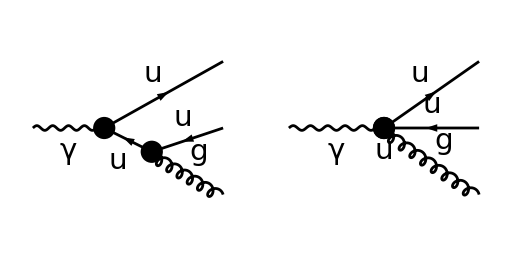

```mathematica
$top = CreateTopologies[0, 1 -> 3];
$diag = InsertFields[$top,{V[1]}->{F[3, {1}], -F[3, {1}],V[5]},
		InsertionLevel -> {Classes}, Model -> "SMQCD", ExcludeParticles -> {S[1], S[2], V[2]}];
Paint[$diag, ColumnsXRows -> {2, 1}, Numbering -> None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
$amp=FCFAConvert[CreateFeynAmp[$diag,Truncated -> False],IncomingMomenta->{q},
OutgoingMomenta->{p1,p2,p3},UndoChiralSplittings->True,DropSumOver->True,List->False,SMP->True]//Contract
```

```mathematica
$amp=ChangeDimension[$amp,n]
```

2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].(DiracGamma[Momentum[p1+p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[q,ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[-Momentum[p1,n]-Momentum[p3,n],SMP[m_u]]] SMP[e] SMP[g_s] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col2],SUNFIndex[Col3]]+2/3 Spinor[Momentum[p1,n],SMP[m_u],1].DiracGamma[Momentum[Polarization[q,ⅈ],n],n].(DiracGamma[Momentum[-p2-p3,n],n]+SMP[m_u]).DiracGamma[Momentum[Polarization[p3,-ⅈ],n],n].Spinor[-Momentum[p2,n],SMP[m_u],1] FeynAmpDenominator[PropagatorDenominator[Momentum[p2,n]+Momentum[p3,n],SMP[m_u]]] SMP[e] SMP[g_s] SUNTF[{SUNIndex[Glu4]},SUNFIndex[Col2],SUNFIndex[Col3]]

```mathematica
SetMandelstam[s,{-q,p1,p2,p3},{1,0,0,0}];
```

```mathematica
$me2=$amp*(ComplexConjugate[$amp]//FCRenameDummyIndices)//
PropagatorDenominatorExplicit//FermionSpinSum//ReplaceAll[#,{DiracTrace->Tr}]&//DoPolarizationSums[#,q,0,VirtualBoson->True,GaugeTrickN->4]&//DoPolarizationSums[#,p3,0]&;
```

```mathematica
$r1=$me2//SUNSimplify[#,SUNNToCACF->False]&;
```

```mathematica
$r2=$r1/.{SUNN->3,SMP["m_u"]->0,SMP["g_s"]->1,SMP["e"]->1}
```

(64 n s[2,3])/(9 s[3,4])-(32 n^2 s[2,3])/(9 s[3,4])+(256 (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 s[3,4])-(128 n (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 s[3,4])+(128 n (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 s[3,4])-(64 n^2 (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 s[3,4])+(1024 s[2,3] (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)-(512 n s[2,3] (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)+(512 n (-s[2,3]-s[3,4]) (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)-(256 n^2 (-s[2,3]-s[3,4]) (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)+(1024 (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]) s[3,4])/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)-(512 n (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]) s[3,4])/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2)+(1024 s[2,3])/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(512 n s[2,3])/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(64 n^2 s[2,3])/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(1024 (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(256 n (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(3 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(128 n^2 (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(512 (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(256 n (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(256 s[2,3]^2)/(3 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(256 n s[2,3]^2)/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(512 s[2,3] (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(3 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(512 n s[2,3] (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(512 s[2,3] (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(256 n s[2,3] (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(3 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(128 n^2 s[2,3] (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(512 s[2,3] (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(256 n s[2,3] (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(512 s[2,3] (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(256 n s[2,3] (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(1024 (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]) (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(512 n (1/2-1/4 s[1,2]-1/4 s[1,4]-1/4 s[2,3]-1/4 s[3,4]) (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(512 n (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]) (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(256 n^2 (-1/2+1/4 s[1,2]+1/4 s[1,4]-1/4 s[2,3]+1/4 s[3,4]) (1/2 s[2,3]+1/2 s[3,4]))/(9 s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))

```mathematica
$res =9/4 $r2/.{n->4-2ep,Rule[Explicit,False]->Rule[Explicit,True]}//Expand//SUNSimplify[#,SUNNToCACF->False]&
```

-16+32 ep-16 ep^2+32/s[3,4]-(64 ep)/s[3,4]+(32 ep^2)/s[3,4]-(16 s[1,2])/s[3,4]+(32 ep s[1,2])/s[3,4]-(16 ep^2 s[1,2])/s[3,4]-(16 s[1,4])/s[3,4]+(32 ep s[1,4])/s[3,4]-(16 ep^2 s[1,4])/s[3,4]-(16 s[2,3])/s[3,4]+(32 ep s[2,3])/s[3,4]-(16 ep^2 s[2,3])/s[3,4]+(128 s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(256 ep s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep^2 s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[1,2] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[1,2] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[1,2] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[1,4] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[1,4] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[1,4] s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[2,3]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[2,3]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[2,3]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(256 ep s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep^2 s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[1,2] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[1,2] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[1,2] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[1,4] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[1,4] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[1,4] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(128 s[2,3] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(256 ep s[2,3] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(128 ep^2 s[2,3] s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 s[3,4]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep s[3,4]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2-(64 ep^2 s[3,4]^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])^2+(128 ep)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])-(128 ep^2)/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])-(64 ep s[1,2])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])+(64 ep^2 s[1,2])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])-(64 ep s[1,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])+(64 ep^2 s[1,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])-(128 ep s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])+(128 ep^2 s[2,3])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])-(128 s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(128 ep s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(64 s[1,2] s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(64 ep s[1,2] s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(64 s[1,4] s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(64 ep s[1,4] s[2,3])/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(64 s[2,3]^2)/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))+(64 ep s[2,3]^2)/(s[3,4] (-2+s[1,2]+s[1,4]+s[2,3]+s[3,4]))-(64 ep s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])+(64 ep^2 s[3,4])/(-2+s[1,2]+s[1,4]+s[2,3]+s[3,4])

```mathematica
Put[$res/.SUNN->3,"~/src/eec@nlo/real/me2/test/a2qqg_0_0.m"]
```